```mathematica
(* Proper derivation of radial scalar projection from vector form is possibly very tricky? *)

ClearAll["Global`*"]
Clear["Global`*"]
$Pre=.  (*clear the prior definition for $Pre*)
echo=Function[main,Unevaluated[main]/.Set->Function[,Print@HoldForm[#=#2];#=#2,HoldFirst],HoldAll];

(* Subscript[e, r][t_] = {Cos[φ[t]], Sin[φ[t]]}; *)
(* Subscript[e, r][t_] :={Subscript[e, rx][t],Subscript[e, ry][t]}
Subscript[e, φ][t_] :={Subscript[e, φx][t],Subscript[e, φy][t]}

r[t_] :=ρ[t] Subscript[e, r][t]
$Assumptions := {{GM, ρ, φ, t} ∈ ℝ, p > -2}

(* ω[t_] = φ'[t]; *)
ϵ[t_] := φ''[t]
Subscript[e, r][t].Subscript[e, φ][t] == 0;


Subscript[e, r]'[t_] = Subscript[e, φ][t] ω[t];
Subscript[e, φ]'[t_] = -Subscript[e, r][t] ω[t];

ϵ[t_] = φ''[t];
(* Subscript[a, r][t_]=r''[t] * Subscript[e, r][t] *)
(* Subscript[a, t][t_]=(r''[t] * Subscript[e, r][t])  *)
(* TODO how to vectorize back? *)

Expand[r''[t]·Subscript[e, r][t] ]*)
```

ω[t_]=T0/ρ[t]^2

T0s=ρ0^2 ω0

(u ⅆu)/ⅆρ==T0^2/ρ^3-GM/ρ^2

eq21=u^2/2==C1-T0^2/(2 ρ^2)+GM/ρ

{{C1→(T0^2-2 GM ρ0)/(2 ρ0^2)}}

eq3=-ρ/(δ √(-T0^2+2 GM ρ+2 C1 ρ^2))==t'[ρ]

y[ρ_]=GM/(2 C1)+ρ

C2s=-(2 GM^2)/C1-4 T0^2

eq4=(GM-2 C1 y)/(C1 √(C2+8 C1 y^2) δ)==t'[y]

sol4={{t[y]→C[1]+(-1/4 √(C2+8 C1 y^2)+(GM Log[4 C1 y+√2 √C1 √(C2+8 C1 y^2)])/(2 √2 √C1))/(C1 δ)}}

t[ρ_]=C3+(-√C1 √(C2+8 C1 (GM/(2 C1)+ρ)^2)+√2 GM Log[4 C1 (GM/(2 C1)+ρ)+√2 √C1 √(C2+8 C1 (GM/(2 C1)+ρ)^2)])/(4 C1^(3/2) δ)

sol5={{C3→(√C1 √(C2+8 C1 (GM/(2 C1)+ρ0)^2)-√2 GM Log[4 C1 (GM/(2 C1)+ρ0)+√2 √C1 √(C2+8 C1 (GM/(2 C1)+ρ0)^2)])/(4 C1^(3/2) δ)}}

C3s=(√C1 √(C2+8 C1 (GM/(2 C1)+ρ0)^2)-√2 GM Log[4 C1 (GM/(2 C1)+ρ0)+√2 √C1 √(C2+8 C1 (GM/(2 C1)+ρ0)^2)])/(4 C1^(3/2) δ)

δ=1

ω0=1

ρ0=1

GM=2

C3=(√C1 √(8 (1+1/C1)^2 C1+C2)-2 √2 Log[4 (1+1/C1) C1+√2 √C1 √(8 (1+1/C1)^2 C1+C2)])/(4 C1^(3/2))

T0=1

C1=-3/2

C2=4/3

Simplify::fas: Warning: one or more assumptions evaluated to False.

t[ρ_]=(2 π+√(-3+12 ρ-9 ρ^2)-2 ⅈ Log[2]+2 ⅈ Log[4-6 ρ+2 ⅈ √(-3+12 ρ-9 ρ^2)])/(3 √3)

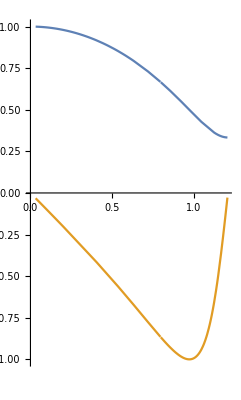

```mathematica
(* Derivation t[ρ], correct, but not interpretable much *)

ClearAll["Global`*"]
Clear["Global`*"]
$Pre=.(*clear the prior definition for $Pre*)
echo=Function[main, Unevaluated[main]/.Set -> Function[, Print@HoldForm[#=#2]; #=#2, HoldFirst], HoldAll];

$Assumptions := {{ρ[t], φ, GM, t[y], y[ρ], ρ0, ω0, u[t], C1, C2, C3} ∈ Reals, {t, ρ[t], ρ0}>0}

(* Radial component equation without derive *)
eq1 := ρ''[t] == ρ[t] ω[t]^2 - GM/ρ[t]^2
(* Tangential component solution without derive *)
ω[t_] = T0 / ρ[t]^2; //echo
T0s = ω0 ρ0^2; //echo

(*u[t]  := (ρ')[t] *)
eq2 =  eq1 /. {ρ''[t] ->u ⅆu/ⅆρ, ρ[t] -> ρ}
uu[u_] = eq2⟦1⟧ ⅆρ/ⅆu;
ρρ[ρ_] = eq2⟦2⟧ ⅆρ/ⅆρ;
eq21 =∫uu[u]ⅆu == ∫ρρ[ρ]ⅆρ + C1; //echo

ρ[0] := ρ0
sol = Solve[eq21 /. {u->0, ρ->ρ0}, C1]
C1s = sol⟦1,1,2⟧;

u[ρ_] = δ * u /. Solve[eq21, u]⟦1⟧;
eq3 = 1/u[ρ] == t'[ρ]; //echo (* this is correct *)

y[ρ_] = ρ + GM/(2 C1); //echo
sol = Solve[y[ρ] == y, ρ];
repl = sol⟦1,1⟧;

C2s = -(2 GM^2)/C1 - 4 T0^2; //echo
eq4 = Simplify[Simplify[eq3 /. {t'[ρ]->t'[y], repl}], C2s == C2]; //echo

sol4 = DSolve[eq4, t[y], y]; //echo
t[y_] = Simplify[sol4⟦1,1,2⟧] /. {C[1]->C3};
t[ρ_] = t[y[ρ]]; //echo

sol5 = Solve[t[ρ0] == 0, C3]; //echo
C3s = sol5⟦1,1,2⟧; (* incorrect? *)

t[ρ_] = Simplify[{t[ρ], δ=1, ω0=1, ρ0=1, GM=2, C3=C3s, T0=T0s, C1=C1s, C2=C2s}]⟦1⟧; //echo
ParametricPlot[{{t[ρ], ρ},{t[ρ], 1/t'[ρ]}}, {ρ, 0, 3}]
```

```mathematica
(* Derivation ρ[t] *)

ClearAll["Global`*"]
Clear["Global`*"]
$Pre=.  (*clear the prior definition for $Pre*)
echo=Function[main,Unevaluated[main]/.Set->Function[,Print@HoldForm[#=#2];#=#2,HoldFirst],HoldAll];

$Assumptions := {{ρ,φ,GM, t,y,ρ0,ω0,u} ∈ Reals, t > 0,{ρ,ρ0}>0}

(* Radial component equation without derive *)
eq1 := (ρ'')[t] == ρ[t] ω[t]^2-GM/ρ[t]^2
(* Tangential component solution without derive *)
T0s := ω0 ρ0^2
ω[t_] := T0/ρ[t]^2

 (*u[t]  := (ρ')[t] *)
 (* (ρ'')[t_] :=(u')[t]u[t] *)
(* (ρ'')[t] ->ⅆu u/ⅆρ *)

eq2 =  eq1 /. {(ρ'')[t] ->ⅆu u / ⅆρ, ρ[t] -> ρ}
uu[u_] = eq2⟦1⟧ⅆρ/ⅆu; //echo
pp[ρ_] = eq2⟦2⟧ⅆρ/ⅆρ; //echo
eq21 =∫uu[u]ⅆu==∫pp[ρ]ⅆρ+C1

u[ρ_]=Solve[eq21,u]⟦2⟧⟦1⟧⟦2⟧ ; //echo  (* [[#]]⟦1⟧⟦2⟧ *)

ρ[0] :=ρ0 
C1s=Solve[u[ρ0]==0, C1]⟦1⟧⟦1⟧⟦2⟧; //echo

(* eq3 = 1/u[ρ] ==  (t')[ρ] == ρ^2/((ρ')[ϕ]T0)*)
eq3 =  (u[ρ[ϕ]](ρ[ϕ]^2) )/T0 ==Derivative[1][ρ][ϕ]

(* ρ[0]==ρ0 *)
ρ[ϕ_]=Simplify[ρ[ϕ]/. DSolve[eq3, ρ[ϕ], ϕ]⟦1⟧⟦1⟧]; //echo

ρ[ϕ_] = Simplify[{ρ[ϕ] ,ω0=1, ρ0=1, GM=5, T0=T0s,C1=C1s,C2=C2s}]⟦1⟧; //echo
Plot[ ρ[ϕ],{ϕ,-5,5}]
```

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
ρ[θ_] := 1/(A Cos[θ-C0]+B)
θ[ρ_] = Solve[ρ == ρ[θ], θ]⟦1⟧⟦1⟧⟦2⟧⟦1⟧
θ[ρ_] = θ[ρ] /. Solve[θ[ρ0] == 0, C[1]]⟦1⟧⟦1⟧

(* ρ'[θ] = f(ρ) *)
Simplify[ρ'[θ] /. {θ->θ[ρ]}]
```

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]

T0 := 1; GM = 1;  C1:= 1;
A:=-1; B:=-1; C0 :=0; ρ0:= 1;
myp[ρ_]=(ρ Sqrt[-T0^2+2 GM ρ+2 C1 ρ^2])/T0
orig[ρ_]=-((A Sin[C0+ArcCos[(1-B ρ)/(A ρ)]-ArcCos[(1-B ρ0)/(A ρ0)]])/(B+A Cos[C0+ArcCos[(1-B ρ)/(A ρ)]-ArcCos[(1-B ρ0)/(A ρ0)]])^2)
Plot[{myp[ρ],orig[ρ]} ,{ρ,0,8}]

∫x^(-1/3) ⅆx
```